# QFT compilation

## Toy device

Connectivity

```mathematica
qubitsnum=3;
```

```mathematica
Graph[Range[0,qubitsnum-1],Table[j<->j+1,{j,0,qubitsnum-2}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

-Graphics-

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->40,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.999,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{0,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.999,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{0,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->10
};
```

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

## Modules

```mathematica
SetAttributes[CompileCirc,HoldAll]
CompileCirc[conf_,unitary_,qubitsnum_]:=Module[{iansatz,nansatz,simpncirc,uapprox,uvc,uec,fdist},
{time,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}}=Timing[CircuitSynthesis[qubitsnum,conf]];

iansatz=Reverse[ansatz]/.(-θvars);
nansatz=noisyAnsatz[iansatz,conf];
simpncirc=SimplifyCircuit[DeleteCases[DeleteCases[nansatz,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
uapprox=CalcCircuitMatrix[simpncirc];
(* fidelity distance *)
uvc=Flatten@ConjugateTranspose@unitary;
Print[Length@uapprox,Length@uvc];
uec=#.uvc&/@uapprox;
fdist=Total[Chop[#*Conjugate[#]]&/@uec]/Length@uec;
Print["compile time:",time/60," minutes; total iterations ",fev];
Print@ListPlot[Elist,AxesLabel->{"Successful iteration","Cost"}];
Print@DrawCircuit[iansatz,qubitsnum];
Print["prob(0):",probzeros];
Print["dist_fid=",fdist]
]
```

```mathematica
(*Test for the variety of the initial states *)
checkVariation[dev_,unitary_,ntrainstates_]:=Module[{conf,a},
conf=DefaultConfig[dev,unitary,ntrainstates];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
(*Print[i,":",a];*)
ToString[Reverse@Sort[Length/@a]]
]

checkedConf[dev_,unitary_,ntrainstates_]:=Module[{conf,a},
While[True,
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,ntrainstates];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
If[AllTrue[Length/@a,#==1&],
Break[]]
];
conf
]
```

## Compilation : QFT

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
```

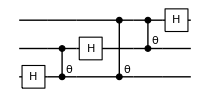

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
```

```mathematica
conf=checkedConf[dev,unitary,5];
```

```mathematica
CompileCirc[conf,unitary,qubitsnum]
```

Compilation with automatically generated ansatz

@cycle1:Thu 15 Sep 2022 19:37:14, fev:439, <E>: 0.21507513181850468 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 0, 1}

@cycle2:Thu 15 Sep 2022 19:39:45, fev:868, <E>: 0.18278615485790403 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 0, 1}

@cycle3:Thu 15 Sep 2022 19:43:13, fev:1363, <E>: 0.16266715661410958 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 0, 2}

@cycle4:Thu 15 Sep 2022 19:46:44, fev:1588, <E>: 0.13424483973946794 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 0, 4}

@cycle5:Thu 15 Sep 2022 19:50:35, fev:1962, <E>: 0.08417304856471526 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 2, 7}

@cycle6:Thu 15 Sep 2022 19:53:05, fev:2386, <E>: 0.07156345681557248 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 51, 0, 2, 7}

@cycle7:Thu 15 Sep 2022 19:54:10, fev:2513, <E>: 0.06701455538323439 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 53, 0, 2, 8}

@cycle8:Thu 15 Sep 2022 19:58:06, fev:2747, <E>: 0.055318884991477656 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 63, 0, 2, 8}

$Aborted